## Replicate Planck Plot

```mathematica
makeLegendEntry[col_,mark_,lab_]:=Module[{leg},
leg=Text[StringForm["``     ``",Style[mark,col],lab]];
Return[leg]];
```

### Planck Constraint Contour

```mathematica
makePlanckContours[nsmin_,nsmax_,rmin_,rmax_]:=Module[{ns0,r0,radns,radr,radns2,radr2,col,plt,leg},
col=ColorData[97,"ColorList"][[1]];
ns0=0.9642; r0=0; radns=0.008182; radr=0.06379; radns2=0.012545; radr2=0.12759;
plt=ParametricPlot[{{radns*r* Cos[t]+ns0,radr*r*Sin[t]+r0},{radns2*r* Cos[t]+ns0,radr2*r*Sin[t]+r0}},{t,-Pi,Pi},{r,0,1},PlotRange->{{nsmin,nsmax},{rmin,rmax}},PlotStyle->col,AspectRatio->Full,BoundaryStyle->col,FrameLabel->{Style["n_s",FontSize->24],Style["r",FontSize->24]},FrameStyle->Directive[FontSize->18]];
leg=makeLegendEntry[col,■,"Planck 2015 TT,TE,EE+lowP"];
Return[{plt,leg}]];
```

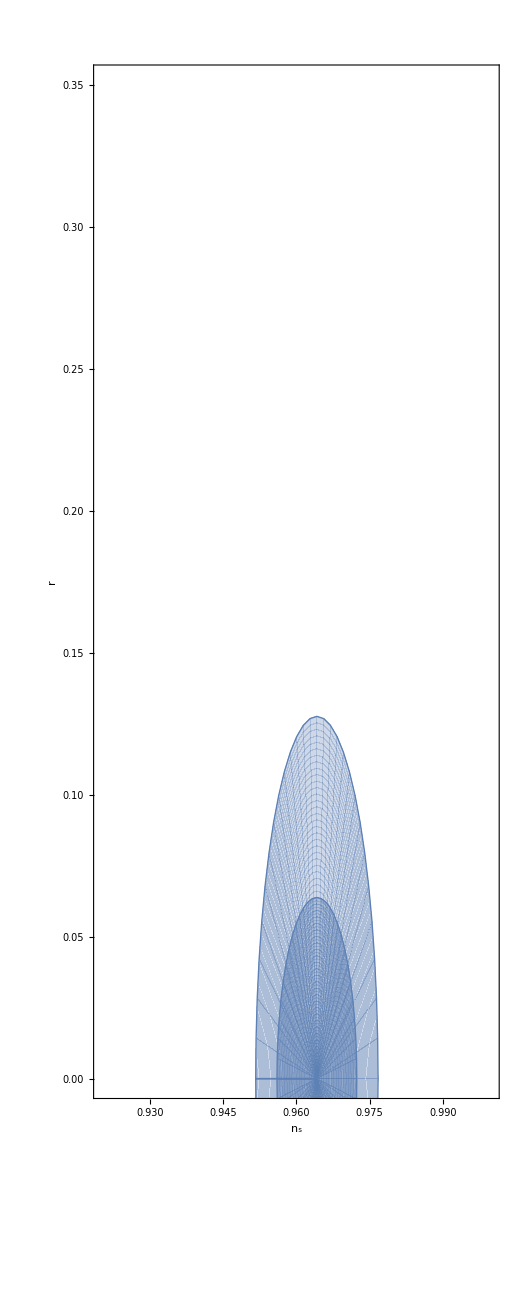

■     Planck 2015 TT,TE,EE+lowP

```mathematica
{plnkCont,plnkLeg}=makePlanckContours[0.92,1,0,0.35];
Show[plnkCont]
plnkLeg
```

### Plotting Modules

```mathematica
plotPotential[va_,left_,aList_,mark_,col_,lab_]:=Module[{p1,p2,p3,plt,ns60List,ns50List,r60List,r50List,ni,nf,ni2,nf2,n1guess,ϕsol2,ns,r,ϵ2,v,nsmin,nsmax,rmin,rmax,leg},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];

ni = 80; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsolnfLoop[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left,0.2],Print["ABORTED"];Continue[]];
{ns,r,ϵ2} = findNsR[v,v',ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}];
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Transpose[{ns60List,r60List}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,20},PlotStyle->col];
p2 = ListPlot[Transpose[{ns50List,r50List}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,12},PlotStyle->col];
plt=Show[p1,p2];
leg=makeLegendEntry[col,mark,lab];
Return[{plt,leg}]];
```

```mathematica
plotPotentialLines[va_,left_,aList_,col_,lab_]:=Module[{p1,ns60List,ns50List,r60List,r50List,ni,nf,ni2,nf2,n1guess,ϕsol2,ns,r,ϵ2,v,nsmin,nsmax,rmin,rmax,leg,divList,jj},
ns60List={};ns50List={};r60List={};r50List={};
divList=Delete[FindDivisions[{1,Length[aList]},10],1];jj=1;
Print[divList];
Do[
v[x_]:=va[x,aList[[ii]]];

ni = 80; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsolnfLoop[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left,0.2],Print["ABORTED"];Continue[]];
{ns,r,ϵ2} = findNsR[v,v',ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
If[ii==divList[[jj]],Print["."];jj++];
,{ii,1,Length[aList]}];
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1=ListLinePlot[Transpose[{Transpose[{ns50List,r50List}],Transpose[{ns60List,r60List}]}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->Directive[Opacity[0.3,col],Thickness[0.02]]];
leg=makeLegendEntry[col,■,lab];
Return[{p1,leg}]];
```

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

{10.,10.3495,10.7113,11.0857,11.4731,11.8741,12.2892,12.7187,13.1633,13.6233,14.0995,14.5923,15.1024,15.6302,16.1765,16.742,17.3271,17.9328,18.5596,19.2083,19.8796,20.5745,21.2936,22.0379,22.8081,23.6053,24.4304,25.2843,26.1681,27.0827,28.0293,29.009,30.0229,31.0723,32.1584,33.2824,34.4457,35.6497,36.8957,38.1853,39.52,40.9013,42.3309,43.8105,45.3418,46.9266,48.5668,50.2643,52.0212,53.8394,55.7212,57.6688,59.6845,61.7706,63.9297,66.1642,68.4768,70.8702,73.3473,75.911,78.5643,81.3103,84.1523,87.0936,90.1377,93.2883,96.5489,99.9236,103.416,107.031,110.772,114.644,118.651,122.798,127.09,131.532,136.129,140.887,145.812,150.908,156.183,161.642,167.292,173.139,179.191,185.454,191.936,198.644,205.587,212.773,220.21,227.907,235.873,244.117,252.65,261.481,270.62,280.079,289.868,300.}

{10,20,30,40,50,60,70,80,90,100}

.

.

.

«7 more identical outputs»

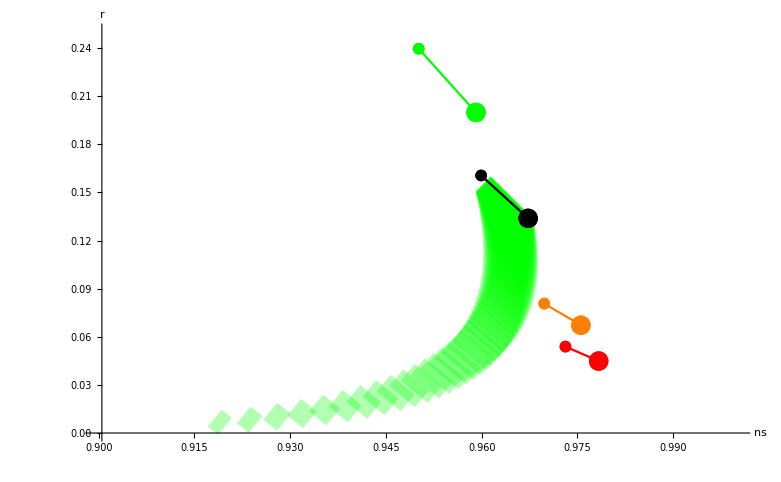

■     Hilltop: V=λ(ϕ^2  - σ^2)^2

```mathematica
v[x_,a_]:=(0.01)*((x^2-(a)^2)^2 );
left=True;
aList =Join[Range[10,15,0.15],Range[15,25,0.5],Range[20,60,2]];
aList=logspace[10,300,100,10.]
(*{10,10.5,11,11.5,12,13,14,15,16,17,20,21,22,25,26,30,40,50,60,70,80,100};*)
{p1,leg1} = plotPotentialLines[v,left,aList,Green,"Hilltop: V=λ(ϕ^2  - σ^2)^2"];
Show[p1,plotList]
leg1
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

{8.,8.20673,8.41879,8.63634,8.85951,9.08844,9.32329,9.56421,9.81136,10.0649,10.325,10.5918,10.8655,11.1462,11.4343,11.7297,12.0328,12.3438,12.6628,12.99,13.3256,13.67,14.0232,14.3856,14.7573,15.1387,15.5299,15.9312,16.3428,16.7651,17.1984,17.6428,18.0987,18.5664,19.0461,19.5383,20.0432,20.5611,21.0924,21.6374,22.1966,22.7701,23.3585,23.9621,24.5813,25.2165,25.8681,26.5366,27.2223,27.9258,28.6474,29.3876,30.147,30.9261,31.7252,32.545,33.386,34.2487,35.1337,36.0416,36.9729,37.9283,38.9084,39.9139,40.9453,42.0033,43.0887,44.2021,45.3443,46.5161,47.7181,48.9511,50.2161,51.5137,52.8448,54.2104,55.6112,57.0482,58.5224,60.0347,61.586,63.1774,64.81,66.4847,68.2027,69.9651,71.773,73.6277,75.5303,77.482,79.4842,81.5381,83.6451,85.8066,88.0239,90.2985,92.6318,95.0255,97.481,100.}

{10,20,30,40,50,60,70,80,90,100}

.

.

.

«18 more identical outputs»

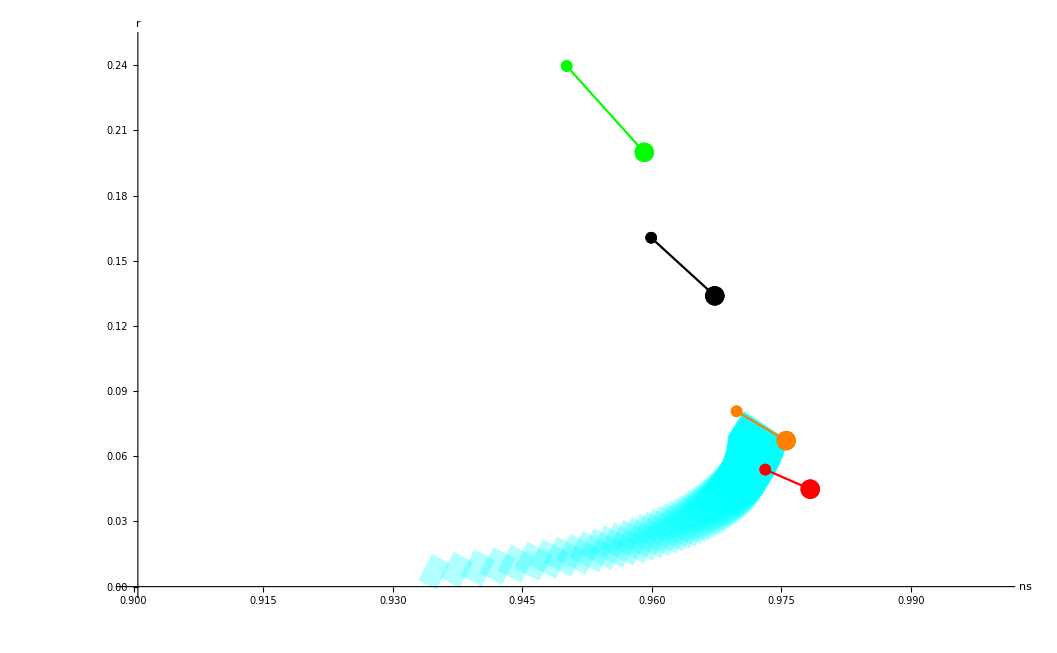

■     Hilltop: V=λ(1 - TraditionalForm` )

```mathematica
v[x_,a_]:=(0.01)*(1-(x/a)^2);
left=True;
(*aList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};*)
aList =Join[Range[8,15,0.25],Range[15,25,1],Range[20,60,10]];
aList=logspace[8,100,100,10.]
{p2,leg2} = plotPotentialLines[v,left,aList,Cyan,"Hilltop: V=λ(1 - TraditionalForm` )"];
Show[p2,plotList]
leg2
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

{10,20,30,40,50,60,70,80,90,100}

.

.

.

«7 more identical outputs»

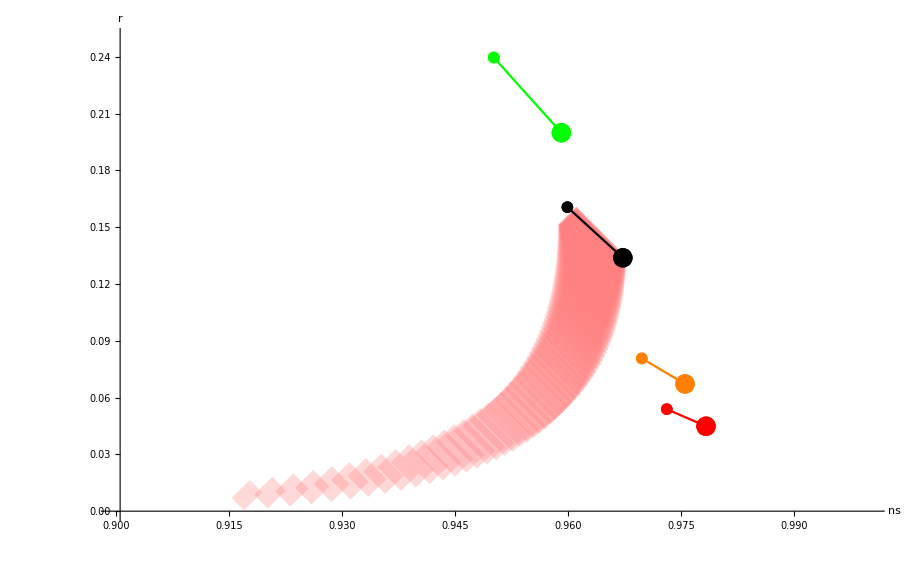

■     Natural Inflation Models: V=λ(1 + CosTraditionalForm` )

```mathematica
v[x_,a_]:= 0.5*(0.01)*(1+Cos[x/a]);
left=True;
(*aList = {5,7,10,12,15,17,20,22,25};*)
(*aList=Join[Range[2,7,0.05],Range[7,10,0.5],Range[10,15,1]];*)
aList=logspace[3.5,30,100,10.];
{p3,leg3}=plotPotentialLines[v,left,aList,Pink,"Natural Inflation Models: V=λ(1 + CosTraditionalForm` )"];
Show[p3,plotList]
leg3
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

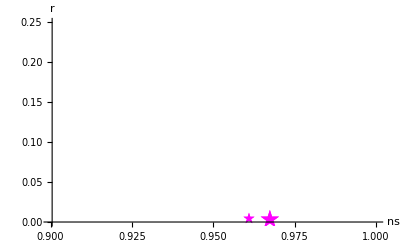

★     Starobinsky'sTraditionalForm`Model:TraditionalForm`

```mathematica
v[x_,a_]:=(0.1)*(1-Exp[-a*x])^2;
left=False;
aList={√(2/3)};
{p4,leg4}=plotPotential[v,left,aList,★,Magenta,"Starobinsky'sTraditionalForm`Model:TraditionalForm`"];
Show[p4]
leg4
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

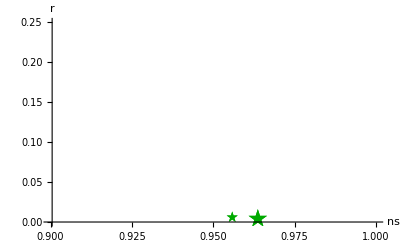

★     Shaposhnikov's Model: TraditionalForm`V

```mathematica
v[x_,a_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
left=False;
aList={2/√6};
{p5,leg5}=plotPotential[v,left,aList,★,Darker[Green],"Shaposhnikov's Model: TraditionalForm`V"];
Show[p5]
leg5
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

{2,4,6,8,10,12,14}

.

.

.

«6 more identical outputs»

{2,4,6,8,10,12,14}

.

.

.

«7 more identical outputs»

{2,4,6,8,10,12,14}

.

.

.

«6 more identical outputs»

{2,4,6,8,10,12,14}

.

.

.

«7 more identical outputs»

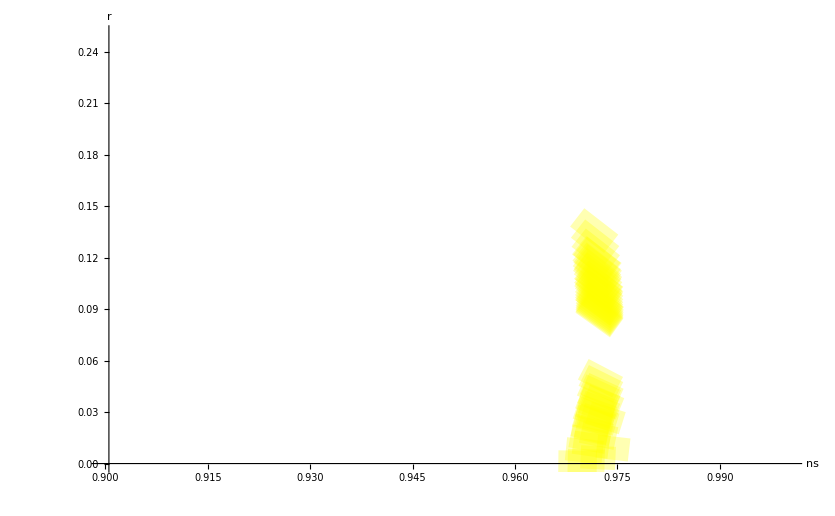

■     D-brane: V=λ^4(1-(a/ϕ)^p)

```mathematica
pList={1,2,3,4};
(*cList = {Red,Green,Blue,Orange}; *)
p6lst={};
Do[v[x_,a_]:=(0.01)*(1-(a/x)^pList[[jj]]);
left=False;
(*aList = {1,10,20,30,70,80,90,100};*)
aList=Join[Range[1,30,5],Range[70,100,5]];
{p6,leg6}=plotPotentialLines[v,left,aList,Yellow,StringForm["D-brane: V=λ^4(1-(a/ϕ)^p)",ToString[pList[[jj]]]]];
AppendTo[p6lst,p6];
,{jj,1,Length[pList]}];
Show[p6lst]
leg6
```

### Exponential Models: V=λ(1-e^-qϕ)

{0.01,0.011721,0.0137382,0.0161026,0.0188739,0.0221222,0.0259294,0.030392,0.0356225,0.0417532,0.048939,0.0573615,0.0672336,0.0788046,0.0923671,0.108264,0.126896,0.148735,0.174333,0.204336,0.239503,0.280722,0.329034,0.385662,0.452035,0.529832,0.621017,0.727895,0.853168,1.}

{5,10,15,20,25,30}

.

.

.

«12 more identical outputs»

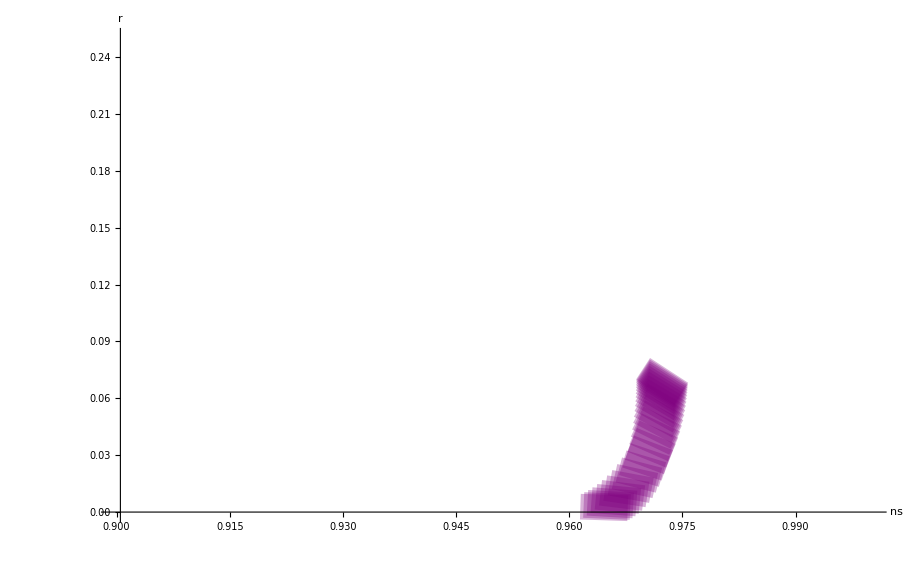

■     Exponential: V=λ(1-e^-qϕ)

```mathematica
v[x_,a_]:=(0.01)*(1-Exp[-a*x]);
left=False;
aList = Range[0.05,1,0.05]; (*{0.01,0.05,0.1,0.5,1}*)
aList=logspace[0.01,1,30,10.]
{p7,leg7} = plotPotentialLines[v,left,aList,Purple,"Exponential: V=λ(1-e^-qϕ)"];
Show[p7]
leg7
```

### Spontaneously Broken SUSY: V(ϕ)=λ^4(1+a*log[ϕ/M_pl])

{2,4,6,8,10,12,14,16,18,20}

.

.

.

«69 more identical outputs»

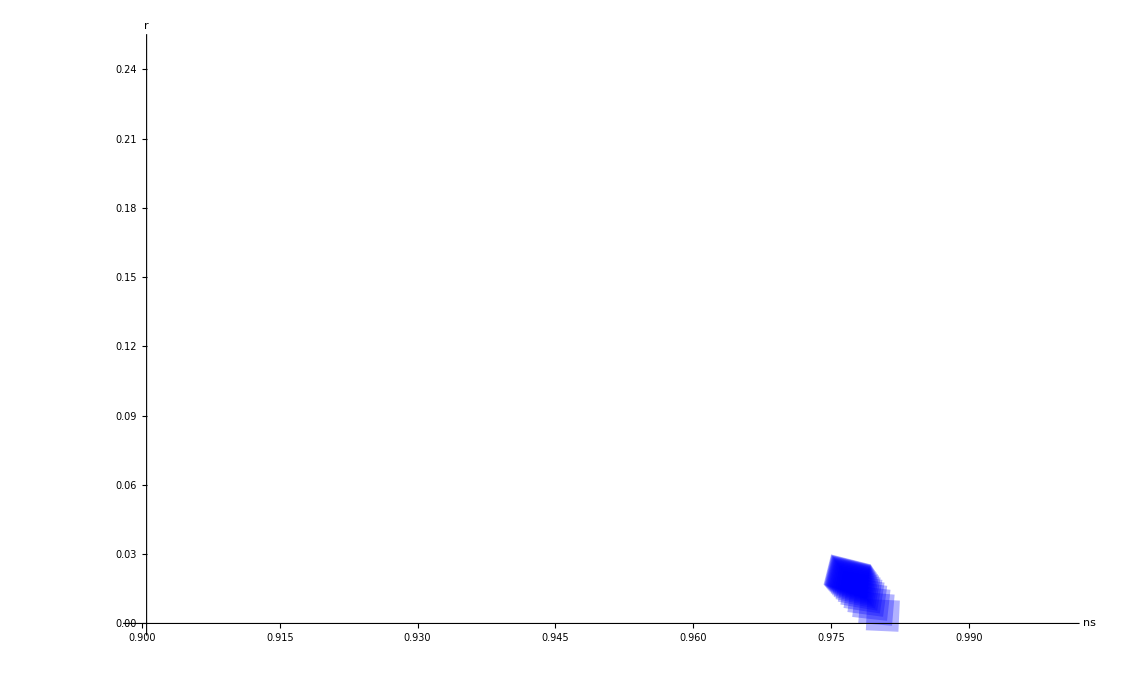

■     SUSY: V=λ(1+a*log[ϕ])

```mathematica
v[x_,a_]:=(0.01)*(1+a*Log[x]);
left=False;
aList = Range[0.05,1,0.05];
{p8,leg8} = plotPotentialLines[v,left,aList,Blue,"SUSY: V=λ(1+a*log[ϕ])"];
Show[p8]
leg8
```

## Monomial Loop for Planck Plot

ϕ0list = {-1.41421,0,1.41421}

vacuumArray = {0}

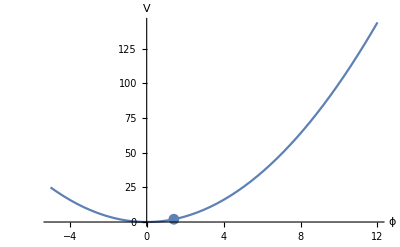

roots = {n→-1.0509}

ϕ0list = {-0.471405,0.471405}

vacuumArray = {}

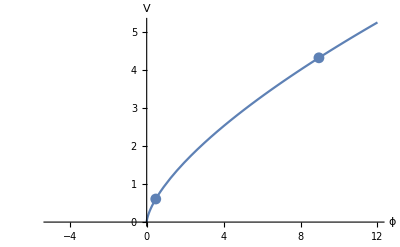

NDSolve::ndsz: At n == -1.61847, step size is effectively zero; singularity or stiff system suspected.

roots = {n→-1.04318}

ϕ0list = {-0.707107,0.707107}

vacuumArray = {}

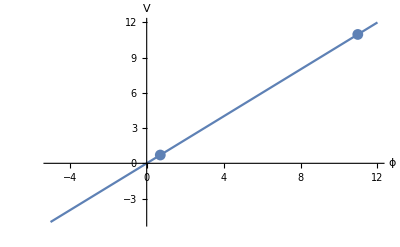

NDSolve::ndsz: At n == -1.39548, step size is effectively zero; singularity or stiff system suspected.

roots = {n→-1.05019}

ϕ0list = {-2.12132,0,2.12132}

vacuumArray = {0}

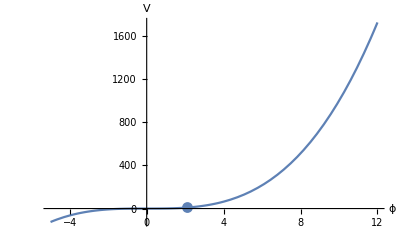

roots = {n→-1.04329}

ϕ0list = {-2.82843,0,2.82843}

vacuumArray = {0}

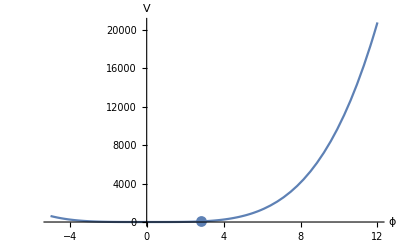

roots = {n→-1.03386}

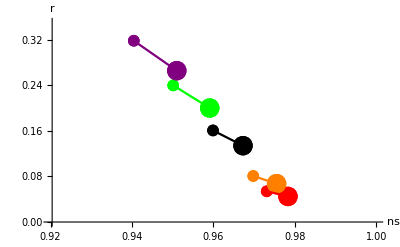

●     Monomial: V=λϕ^2
●     Monomial: V=λϕ^(2/3)
●     Monomial: V=λϕ^1
●     Monomial: V=λϕ^3
●     Monomial: V=λϕ^4

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; legList={};
clrList = {Black,Red,Orange,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
AppendTo[legList,makeLegendEntry[clrList[[ii]],●,StringForm["Monomial: V=λϕ^(``)",pList[[ii]]]]];
ii = ii+1,{p,pList}]
Show[plotList]
Column[legList]
```

### Put it all together! :)

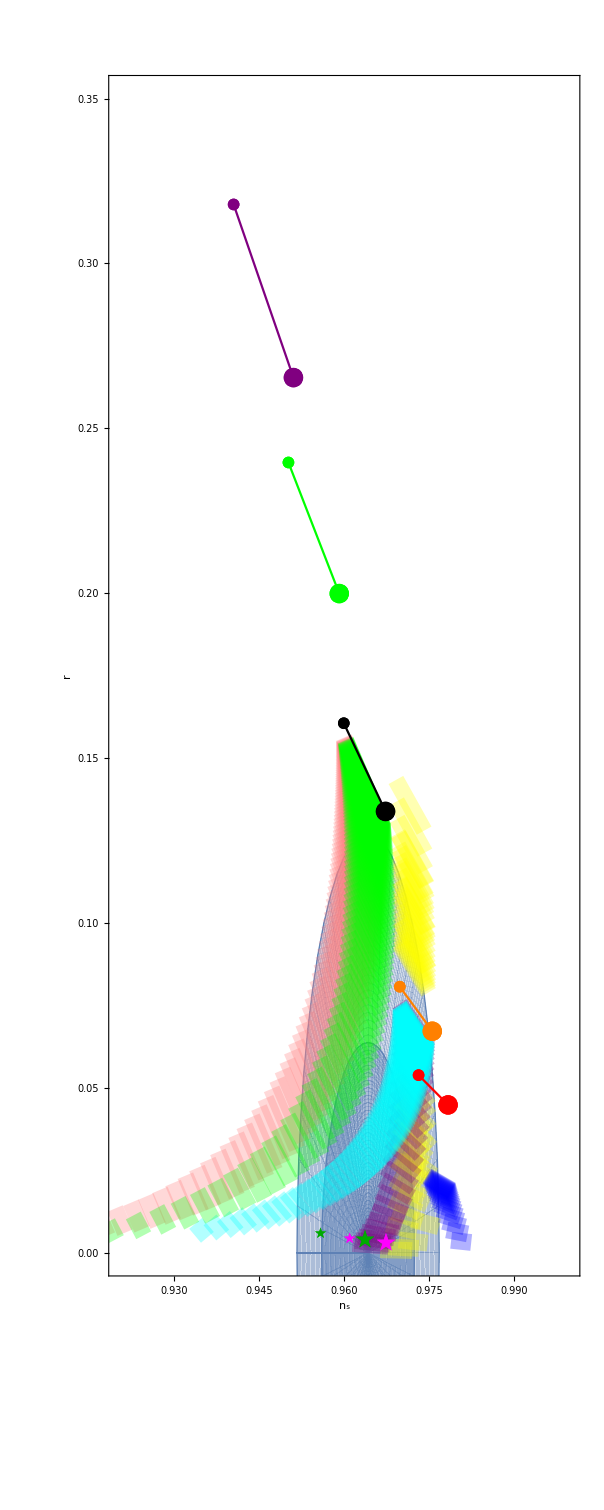

■     Planck 2015 TT,TE,EE+lowP
■     Hilltop: V=λ(ϕ^2  - σ^2)^2
■     Hilltop: V=λ(1 - TraditionalForm` )
■     Natural Inflation Models: V=λ(1 + CosTraditionalForm` )
★     Starobinsky'sTraditionalForm`Model:TraditionalForm`
★     Shaposhnikov's Model: TraditionalForm`V
■     D-brane: V=λ^4(1-(a/ϕ)^p)
■     Exponential: V=λ(1-e^-qϕ)
■     SUSY: V=λ(1+a*log[ϕ])

●     Monomial: V=λϕ^2
●     Monomial: V=λϕ^(2/3)
●     Monomial: V=λϕ^1
●     Monomial: V=λϕ^3
●     Monomial: V=λϕ^4

```mathematica
Show[Join[{plnkCont},p6lst,{p8,p3,p7,p2,p1},{p4,p5},plotList]]
Column[{plnkLeg,leg1,leg2,leg3,leg4,leg5,leg6,leg7,leg8}]
Column[legList]
```